## One. In vitro data.

```mathematica
data = {{1.0009,8.0},{10.009, 91.0},{30.0279,2188.0},{40.0372,3372.0},{50.0465,8126.0},{60.05585,12025.0},{80.0744,18329.0},{100.093,27153.0},{120.1117,31233.0},{200.1861,37986.0},{300.279,39662.0},{1000.930,39967.0},{10009.308,39984.0}};
data = Map[{#[[1]], #[[2]]/40000*100}&, data];
```

```mathematica
Rasterize[ListPlot[data,
AxesLabel->{"N [nM]","Healthy cells [%]"},
Joined->True,
Mesh->Full,
PlotStyle->Directive[ColorData["Legacy","SeaGreen"],PointSize[0.02]],
ScalingFunctions->{"Log"}
]]
```

-Graphics-

## Two. In vivo data, simple delay [half-day encrease].

```mathematica
raw={{39982.0,39855.0,39409.0,38384.0,36556.0,34356.0,31685.0,28990.0,25965.0,22917.0},{39981.0,39856.0,39429.0,38148.0,35510.0,31698.0,26931.0,21936.0,17063.0,12670.0},{39981.0,39778.0,38811.0,35642.0,29773.0,22085.0,14761.0,8719.0,4570.0,2350.0},{39982.0,39763.0,38547.0,34106.0,24752.0,14821.0,7116.0,2975.0,1341.0,546.0},{39982.0,39817.0,38695.0,33351.0,20856.0,8543.0,2793.0,1006.0,172.0,14.0},{39982.0,39766.0,38454.0,32062.0,15722.0,2839.0,203.0,10.0,0.01,0.01},{39983.0,39769.0,38326.0,30935.0,12331.0,1347.0,48.0,3.0,0.01,0.01},{39983.0,39693.0,37552.0,27159.0,6859.0,364.0,15.0,2.0,2.0,0.01},{39984.0,39744.0,38269.0,29930.0,8660.0,370.0,19.0,6.0,2.0,1.0},{39984.0,39697.0,37833.0,27846.0,6354.0,221.0,7.0,1.0,0.01,0.01},{39983.0,39722.0,38114.0,28960.0,7517.0,319.0,15.0,2.0,1.0,1.0},{39982.0,39740.0,38274.0,30056.0,8702.0,404.0,21.0,2.0,0.01,0.01},{39982.0,39730.0,38186.0,29796.0,8690.0,401.0,16.0,2.0,1.0,1.0}};
```

```mathematica
ListPlot[raw,InterpolationOrder->0,
ColorFunction->"BlueGreenYellow", 
Mesh->None,
Frame->True,
DataRange->{0,4.5},
ScalingFunctions->{None,None},
FrameLabel->{"Delay","Surviving healthy cells"},PlotLegends->BarLegend[{"BlueGreenYellow",{0,2}}]]
```

-Graphics-

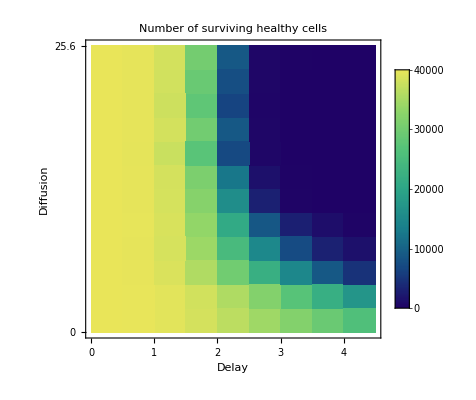

```mathematica
Show[ListDensityPlot[raw,InterpolationOrder->0,
ColorFunction->"BlueGreenYellow", 
Mesh->None,
Frame->True,
ScalingFunctions->{None,None},
DataRange->{{0,4.5},{0,25.6}},
PlotLabel->Style["Number of surviving healthy cells",14, Bold],
FrameTicks->{{{0,25.6},None},{{0,1,2,3,4},None}},
FrameLabel->{"Delay","Diffusion"},
PlotLegends->BarLegend[{"BlueGreenYellow",{0,40000}}]]]
```

```mathematica
MatrixPlot[raw,
PlotLabel->Style["Number of surviving healthy cells",14, Bold],
Frame->True,
ColorFunction->"BlueGreenYellow",
FrameLabel->{"Diffusion","Delay"},
PlotLegends->BarLegend[{"BlueGreenYellow",{0.1,1}}],
FrameTicks->{{ytix,None},{xtix,None}}]
```

-Graphics-

```mathematica
xtix=Array[{#,Rotate[ ToString[Evaluate[0.00625*Power[2,#-1]]],3 Pi/2],{0,0}}&,{13}];
ytix=Array[{#, ToString[Evaluate[(#-1)/2.0]],{0,0}}&,{10}];
```

```mathematica
Rasterize[With[{data=raw},
PointValuePlot[Flatten@MapIndexed[#2->#1&,data,{2}],"Size",BubbleSizes->{0.10,0.10},
PlotLabel->Style["Number of surviving healthy cells",14, Bold],
FrameLabel->{"Diffusion coefficient [sigma square / min]","Treatment delay [days]"},
ColorFunction->"BlueGreenYellow",
AspectRatio->10.0/13,
PlotLegends->BarLegend[{"BlueGreenYellow",{0,40000}}],
FrameTicks->{{ytix,None},{xtix,None}}]]]
```

-Graphics-

## Three. In vivo data.

```mathematica
damageDelayData={{39982.0,36371.0,33942.0,31785.0,29617.0,27545.0,25351.0,23243.0,21215.0,19291.0,17242.0,15294.0,13434.0,11502.0,9744.0,7831.0,6005.0,4558.0,3196.0,1577.0},{39981.0,36060.0,33226.0,30706.0,28352.0,26099.0,23843.0,21747.0,19813.0,17954.0,16105.0,14156.0,12340.0,10646.0,8982.0,7388.0,5861.0,4495.0,3166.0,1394.0},{39981.0,35382.0,32067.0,29262.0,26641.0,24274.0,22085.0,20087.0,18066.0,16149.0,14228.0,12521.0,10829.0,9195.0,7748.0,6221.0,4769.0,3478.0,2314.0,1241.0},{39982.0,34928.0,31123.0,27968.0,25141.0,22796.0,20614.0,18603.0,16523.0,14733.0,13016.0,11322.0,9698.0,8059.0,6573.0,5240.0,4113.0,3031.0,2082.0,1051.0},{39982.0,34536.0,30345.0,26790.0,23704.0,21118.0,18684.0,16434.0,14418.0,12610.0,10909.0,9455.0,7992.0,6716.0,5534.0,4517.0,3530.0,2716.0,1796.0,882.0},{39982.0, 34302.0, 29765.0, 25895.0, 22504.0, 19386.0, 16655.0, 14349.0, 12226.0, 10253.0, 8574.0, 7163.0, 5770.0, 4634.0, 3548.0, 2668.0, 1900.0, 1246.0, 645.0, 291.0}, {39983.0,34041.0,29425.0,25098.0,21636.0,18503.0,15802.0,13492.0,11347.0,9614.0,7905.0,6461.0,5264.0,4107.0,3179.0,2320.0,1598.0,1058.0,550.0,195.0},{39983.0,33963.0,29126.0,24912.0,21098.0,17893.0,15039.0,12731.0,10754.0,8763.0,7181.0,5942.0,4582.0,3459.0,2665.0,1953.0,1322.0,776.0,429.0,169.0},{39984.0,34068.0,28934.0,24477.0,20666.0,17397.0,14610.0,12307.0,10129.0,8346.0,6753.0,5324.0,4228.0,3307.0,2470.0,1698.0,1117.0,741.0,384.0,167.0},{39984.0,33960.0,28937.0,24522.0,20698.0,17376.0,14534.0,12163.0,9958.0,8160.0,6705.0,5340.0,4166.0,3299.0,2439.0,1742.0,1166.0,759.0,405.0,159.0}};
```

```mathematica
damageDelayDataPercent=Map[#/40000*100&,damageDelayData,{2}];
```

```mathematica
xtix=Array[{#,Rotate[ ToString[Evaluate[0.00625*Power[2,#-1]]],3 Pi/2],{0,0}}&,{10}];
ytix=Array[{#, ToString[Evaluate[((#-1)/2)*10]],{0,0}}&,{20}];
```

```mathematica
Rasterize[Show[With[{data=damageDelayDataPercent},
PointValuePlot[Flatten@MapIndexed[#2->#1&,data,{2}],"Size",BubbleSizes->{0.08,0.08},
PlotLabel->Style["Surviving healthy cells [%]",14, Bold],
FrameLabel->{"Diffusion coefficient [sigma square / min]","Damage [%] at the time of intervention"},
ColorFunction->"Temperature",
AspectRatio->20.0/10,
PlotLegends->BarLegend[{"Temperature",{0,100}}],
FrameTicks->{{ytix,None},{xtix,None}}]],Graphics[{EdgeForm[{Dashed,Lighter[Purple,0.5]}],FaceForm[],Rectangle[{5.5,0.5},{6.5,20.5}]}]]]
```

-Graphics-